```mathematica
sigma[k_,alphan_,betan_]=((2k+1)/(2k)*betan/alphan)^(0.5);
```

```mathematica
alpha0 =1.5625;
beta0 = 0.001125;
k0 = 1;
pmin=0.003;
```

```mathematica
r[extrak_] := 1609*(-2*sigma[k0+extrak,alpha0+extrak,beta0]^2*Log[pmin])^0.5
```

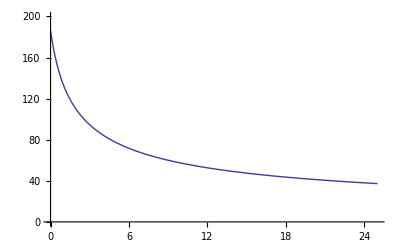

```mathematica
Plot[r[extrak],{extrak,0,25},PlotRange->{0,200}]
```

```mathematica
r[0]
```

180.235